```mathematica
planets = CloudGet["http://wolfr.am/7FxLgPm5"]
```

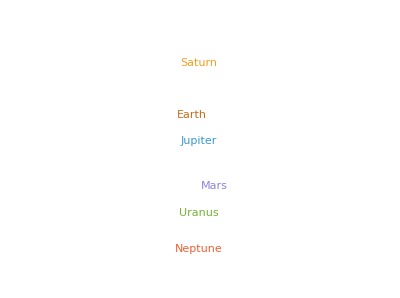

```mathematica
(*45.1*)WordCloud[planets[All,"Moons",Length]]
```

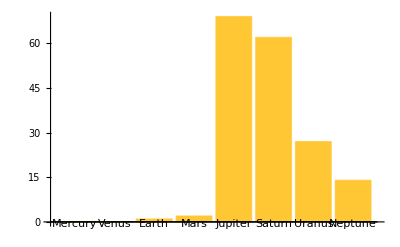

```mathematica
(*45.2*)BarChart[planets[All,"Moons",Length],ChartLabels->Automatic]
```

```mathematica
(*45.3*)planets[SortBy[Length["Moons"]],"Mass"]
```

```mathematica
(*45.4*)planets[All,"Moons",Max,"Mass"]
```

```mathematica
planets[All,"Moons",Total,"Mass"]
```

```mathematica
(*45.6*)planets[All,"Moons",Median,"Mass"]
```

```mathematica
(*45.7*)planets[All,"Moons",Select[#Mass>0.0001["Mass"]&]]
```

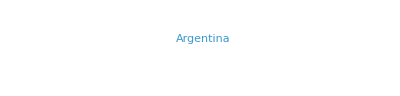
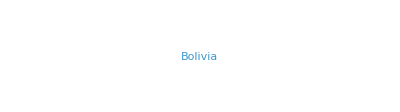
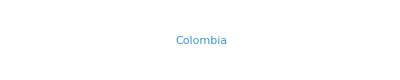
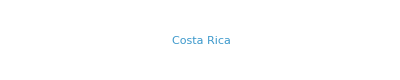
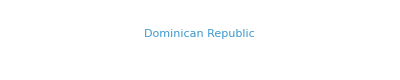
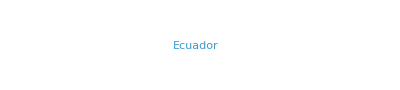
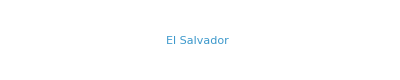
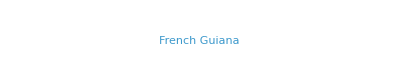
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*45.8*)WordCloud[Association[# -> StringLength[WikipediaData[#]]]]&/@CommonName[EntityList[]]
```

```mathematica
(*45.9, 45.10*)ResourceData["Fireballs and Bolides"][Max,"Altitude"]
ResourceData["Fireballs and Bolides"][TakeLargest[5],"Altitude"]
```

66.6 km

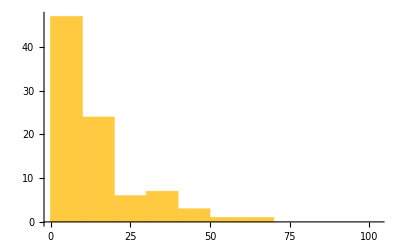

```mathematica
(*45.11*)Histogram[ Differences[ResourceData["Fireballs and Bolides"][All,"PeakBrightness"]]]
```

```mathematica
(*45.12*)GeoListPlot[ ResourceData["Fireballs and Bolides"][1 ;; 10,"NearestCity"]]
```

-Graphics-

```mathematica
(*45.13*)GeoListPlot[ ResourceData["Fireballs and Bolides"][TakeLargestBy[#Altitude &,10],"NearestCity"]]
```

-Graphics-

```mathematica
(*Next chapter*)

(*46.1*)Spectrogram[SpeechSynthesize[Table[StringTemplate["`` million"][i],{i,5}]]]
```

-Graphics-

```mathematica
(*46.2*)Spectrogram[SpeechSynthesize[Last[SortBy[WordList[],StringLength]]]]
```

-Graphics-

```mathematica
(*46.3*)SpeechSynthesize[StringJoin[Riffle[Alphabet[]," "]]]
```

```mathematica
(*46.4*)Spectrogram[SpeechSynthesize[StringJoin[Riffle[Alphabet[]," "]]]]
```

-Graphics-

```mathematica
(*46.5*)AudioPitchShift[SpeechSynthesize["hello"],2]
```

```mathematica
(*46.6*)Table[SpeechRecognize[AudioPitchShift[SpeechSynthesize["computer"],n]],{n,1,1.5,0.1}]
```

{Computer.,Computer.,Computer.,Computer.,Computer.,Thank you, Jack.}

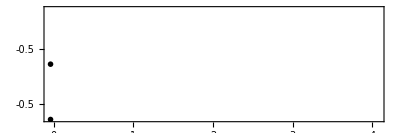

```mathematica
(*46.7*)AudioPlot[Sound[Table[SoundNote[12 n, 1, "Guitar"], {n, 0,3}]]]
```

```mathematica
(*46.8*)Table[AudioIdentify[AudioPitchShift[SoundNote[0, 1, "Trumpet"],n]],{n,0.5,1,0.1}]
```

{trombone,trombone,trombone,trombone,trumpet,trumpet}

```mathematica
(*46.9*)AnimationVideo[Blur[CurrentImage[],20-n],{n,0,20}]
```

```mathematica
(*46.10*)AnimationVideo[Graphics[{Circle[],RegularPolygon[n]}],{n,3,20}]
```

```mathematica
(*46.11*)AnimationVideo[Graphics[Style[Disk[],Hue[n]],ImageSize->50],{n,0,1}]
```

```mathematica
(*46.12*)AnimationVideo[ Rasterize[Style[ToUpperCase[FromLetterNumber[n]],200]],{n,1,26,1}]
```